```mathematica
(*This program is to simulate the population based on 3-state model, including ground state (S0),% excited state (S1) and dark state (D), but not considering reverse DSC*)
ClearAll;
```

```mathematica
Eigensystem[({{-kEx, kEm+kIC, kGSR}, {kEx, -(kEm+kIC+kDSC), 0}, {0, kDSC, -kGSR}})];
```

```mathematica
lambda1=0;
lambda2=0.5 (-kDSC-kEm-kEx-kGSR-kIC-√((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC)));
lambda3=0.5 (-kDSC-kEm-kEx-kGSR-kIC+√((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC)));

v1={(kGSR (kDSC+kEm+kIC))/(kDSC kEx),kGSR/kDSC,1};
v2={-1/(2 kDSC)(kDSC-kEm-kEx+kGSR-kIC-√((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC))),-1/(2 kDSC)(kDSC+kEm+kEx-kGSR+kIC+√((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC))),1};
v3={-1/(2 kDSC)(kDSC-kEm-kEx+kGSR-kIC+√((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC))),-1/(2 kDSC)(kDSC+kEm+kEx-kGSR+kIC-√((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC))),1};
```

```mathematica
(* n[t_]={nS0[t],nS1[t],nD[t]}; *)
nC[c1_,c2_,c3_]:=c1*v1+c2*v2+c3*v3; (* t=0 *)
nBC={1,0,0}; (* Initial condition *)
Solve[nC[c1,c2,c3]==nBC,{c1,c2,c3}];
```

```mathematica
c1=-(√((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC)))/(kDSC (-1/kDSC(√((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC)))-1/kDSC^2 kGSR √((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC))-1/(kDSC kEx)kGSR √((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC))-1/(kDSC^2 kEx)kEm kGSR √((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC))-1/(kDSC^2 kEx)kGSR kIC √((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC))));
c2=-(kDSC kEx (-kDSC-kEm-kEx-kGSR-kIC+√((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC))))/(2 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC) √((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC)));
c3=-(kDSC kEx (kDSC+kEm+kEx+kGSR+kIC+√((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC))))/(2 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC) √((kDSC+kEm+kEx+kGSR+kIC)^2-4 (kDSC kEx+kDSC kGSR+kEm kGSR+kEx kGSR+kGSR kIC)));
nS0[t_]:=c1 Exp[lambda1 t] v1[[1]]+c2 Exp[lambda2 t] v2[[1]]+c3 Exp[lambda3 t] v3[[1]];
nD[t_]:=c1 Exp[lambda1 t] v1[[3]]+c2 Exp[lambda2 t] v2[[3]]+c3 Exp[lambda3 t] v3[[3]];
nS1[t_]:= c1 Exp[lambda1 t] v1[[2]]+c2 Exp[lambda2 t] v2[[2]]+c3 Exp[lambda3 t] v3[[2]];
```

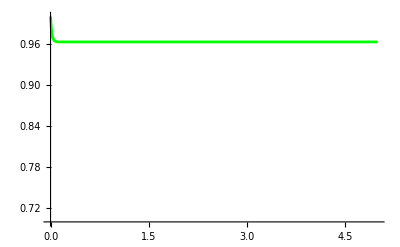

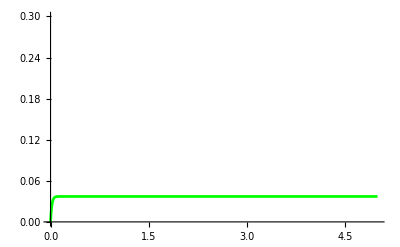

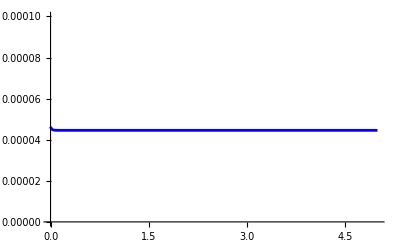

```mathematica
(*Constants*)
h = 6.626*10^-34;
cLight=2.998*10^8;
NA=6.022*10^23;
(*Set parameters*)
lambda=561*10^-9;(* Excitation wavelength in m *)
I0=24*10^4;(* Laser Intensity in W/m^2 (W/cm^2=1e4 W/m^2) *)
QY=0.41;(* Quanutm yield *)
tau=2.45*10^-9;(* Excited state lifetime in sec *)
epsilon=72.9*10^3;(* Molar exctinction coefficient in M^-1cm^-1 at lambda *)
sigma=2.303*epsilon*1*10^3*1*10^-4/NA;(* Absorption cross-section in m^2 *) 
kEx=(I0*sigma*lambda)/(h*cLight);(* Excitation rate,in Hz *)
kEm=QY/tau;(* Radiative emission rate constant,in Hz *)
kDSC=1/(24*10^-6);(* DSC rate constant,in Hz *)
kGSR=1/(20*10^-3);(* GSR rate constant,in Hz *)
kIC=(1/tau)-kEm;(* Non radiative decay rate constant in Hz *)
p1=Plot[nS0[t],{t,0,5}, PlotStyle->Directive[RGBColor[0,1.,0.],AbsoluteThickness[2.]], PlotRange-> {0.7,1.0}]
pD1=Plot[nD[t],{t,0,5}, PlotStyle->Directive[RGBColor[0,1.,0.],AbsoluteThickness[2.]], PlotRange-> {0,0.3}]
p1S1 = Plot[nS1[t],{t,0,5}, PlotStyle->Directive[RGBColor[0,0,1.],AbsoluteThickness[2.]],PlotRange-> {0,0.0001}]
```

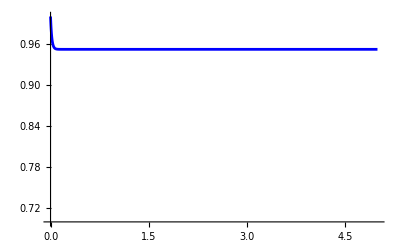

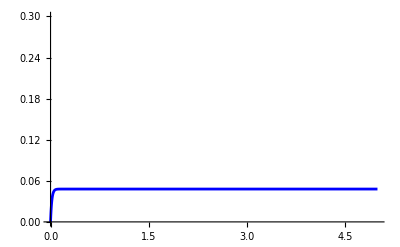

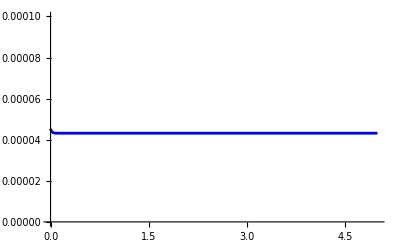

```mathematica
(*Constants*)
h = 6.626*10^-34;
cLight=2.998*10^8;
NA=6.022*10^23;
(*Set parameters*)
lambda=561*10^-9;(* Excitation wavelength in m *)
I0=24*10^4;(* Laser Intensity in W/m^2 (W/cm^2=1e4 W/m^2) *)
QY=0.41;(* Quanutm yield *)
tau=2.40*10^-9;(* Excited state lifetime in sec *)
epsilon=72.9*10^3;(* Molar exctinction coefficient in M^-1cm^-1 at lambda *)
sigma=2.303*epsilon*1*10^3*1*10^-4/NA;(* Absorption cross-section in m^2 *) 
kEx=(I0*sigma*lambda)/(h*cLight);(* Excitation rate,in Hz *)
kEm=QY/tau;(* Radiative emission rate constant,in Hz *)
kDSC=1/(18*10^-6);(* DSC rate constant,in Hz *)
kGSR=1/(20*10^-3);(* GSR rate constant,in Hz *)
kIC=(1/tau)-kEm;(* Non radiative decay rate constant in Hz *)
p2=Plot[nS0[t],{t,0,5}, PlotStyle->Directive[RGBColor[0,0,1.],AbsoluteThickness[2.]], PlotRange-> {0.7,1.0}]
pD2=Plot[nD[t],{t,0,5}, PlotStyle->Directive[RGBColor[0,0,1.],AbsoluteThickness[2.]], PlotRange-> {0,0.3}]
p2S1 = Plot[nS1[t],{t,0,5}, PlotStyle->Directive[RGBColor[0,0,1.],AbsoluteThickness[2.]],PlotRange-> {0,0.0001}]
```

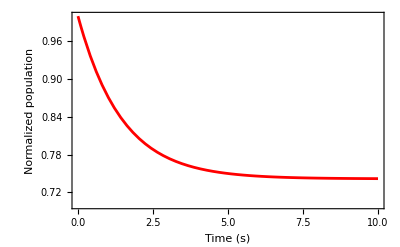

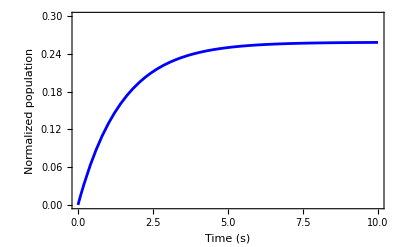

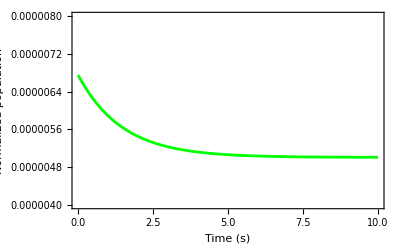

```mathematica
(*Constants*)
h = 6.626*10^-34;
cLight=2.998*10^8;
NA=6.022*10^23;
(*Set parameters*)
lambda=561*10^-9;(* Excitation wavelength in m *)
I0=4.4*10^4;(* Laser Intensity in W/m^2 (W/cm^2=1e4 W/m^2) *)
QY=0.20;(* Quanutm yield *)
tau=2.01*10^-9;(* Excited state lifetime in sec *)
epsilon=70.7*10^3;(* Molar exctinction coefficient in M^-1cm^-1 at lambda *)
sigma=2.303*epsilon*1*10^3*1*10^-4/NA;(* Absorption cross-section in m^2 *) 
kEx=(I0*sigma*lambda)/(h*cLight);(* Excitation rate,in Hz *)
kEm=QY/tau;(* Radiative emission rate constant,in Hz *)
kDSC=1/(38.12*10^-6);(* DSC rate constant,in Hz *)
kGSR=1/(1.9678);(* GSR rate constant,in Hz *)
kIC=(1/tau)-kEm;(* Non radiative decay rate constant in Hz *)
p3=Plot[nS0[t],{t,0,10}, PlotStyle->Directive[RGBColor[1.,0.,0.],AbsoluteThickness[2.]], BaseStyle->{FontSize->18},PlotRange-> {0.70,1.0},Frame->True,FrameLabel->{"Time (s)","Normalized population"}]
pD3=Plot[nD[t],{t,0,10}, PlotStyle->Directive[RGBColor[0.,0.,1.],AbsoluteThickness[2.]], BaseStyle->{FontSize->16},PlotRange-> {0,0.3},Frame->True,FrameLabel->{"Time (s)","Normalized population"}]
p3S1= Plot[nS1[t],{t,0,10}, PlotStyle->Directive[RGBColor[0.,1.,0.],AbsoluteThickness[2.]], BaseStyle->{FontSize->16},PlotRange-> {0.000004,0.000008},Frame->True,FrameLabel->{"Time (s)","Normalized population"}]
```

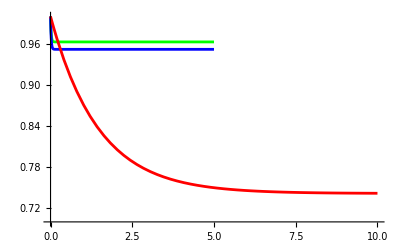

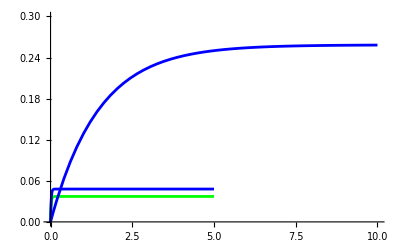

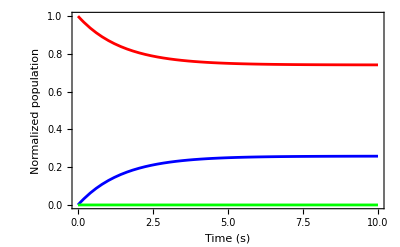

```mathematica
Show[p1,p2,p3, PlotRange-> {0.70,1.0}]
Show[pD1,pD2,pD3, PlotRange-> {0,0.3}] 
Show[p3,pD3, p3S1, PlotRange->{0,1}]
```